```mathematica
NotebookDirectory[]
```

/Users/john/src/TRACIS/Mathematica/

```mathematica
ParallelNeeds["Bem2D`"];
Needs["Bem2D`"];
Needs["LocalUtilities`"];
Needs["PrintLog`"];
Needs["XTracer`"];
```

```mathematica
System`SetSystemOptions["LibraryLinkOptions"->"TestFloatingPointExceptions"->False];
```

```mathematica
{segments,potentials,charges}=solveModel[cefiModel];
```

```mathematica
SetOptions[cefiModel,"vMcp"->-1500.];
```

```mathematica
opts=Options@cefiModel;
scale="scale"/.opts;
{zMcpBottom,zMcpTop,zSkin0,zSkin1,rShutterGrid,zShutterGridTop,rFlatGrid,zFlatGridTop,rMcp,rOuter,rSkin,rInner}=scale*{"zMcpBottom","zMcpTop","zSkin0","zSkin1","rShutterGrid","zShutterGridTop","rFlatGrid","zFlatGridTop","rMcp","rOuter","rSkin","rInner"}/.opts;
zEntrance0=Mean[{zSkin0,zSkin1}];
```

```mathematica
"vMcp"/.opts
```

-1500.

```mathematica
cefiPotentials=cefiPotentialPlot[cefiModel];
```

```mathematica
aperturePotentials=cefiPotentialPlot[cefiModel,"xrange"->{8,12},"zrange"->{9,12},PlotPoints->50,Contours->-Reverse@{.001,.01,.1,1,2,3,4,5,6,7,8,9,10,20,30,40,50,60,70,71,72,73,74,75,76,77,78,79,79.9,79.99,79.999},ContourLabels->None,"CefiPotentialPlotFile"->FileNameJoin[{$UserBaseDirectory,"Applications","Bem2D","CefiAperturePotentialsContourPlot.mmaz"}]];
```

```mathematica
initializeTracer[cefiModel,NotebookDirectory[]<>"eField_loRes_20130423.mmaz"]
```

```mathematica
setElectricFieldInterpolation[cefiModel,NotebookDirectory[]<>"eField_loRes_20130423.mmaz","fieldScaleFactor"->1]
```

```mathematica
Manipulate[Module[{px,pz,count,v,qoverm=1.6*^-19/2.67*^-26,zbot=zMcpBottom,energies}
,
{px,pz}=point/1000.;
v=Speed[en,16.]*1000.;
SetOptions[cefiModel,"vMcp"->vMcp];
     setAnalyzerParameters[cefiModel];
res=trace[{{px,0.,pz}},{v{-Cos[α Degree],0.,Sin[α Degree]}},qoverm];
count=Round@res[[1,1,1]];Show[cefiPotentials,ListPlot[1000Chop[res[[1,All,{2,4}]][[2;;count+1]]],PlotRange->Full,Joined->!showpoints],PlotRange->{{-10,30},{(zbot)*1000,15}},ImageSize->Full]],
{{res,{}},ControlType->None},
{{point,{30.,1000zEntrance0}},Locator},{{en,Energy[7.6,16.]},0.01,25.,Appearance->"Labeled"},{{α,0.},-5.,5.,Appearance->"Labeled"},{{vMcp,-1000},-2400,-1000,Appearance->"Labeled"},{{showpoints,False,"Show points"},{False,True}},TrackedSymbols->{en,α,point,showpoints}]
```

```mathematica
Manipulate[Module[{px,pz,counts,v,charge=1.602*^-19,mass=16.,qoverm,zbot=zMcpBottom,energies,ioncolor,calloutcolor,res,trajectories,x1=9,x2=10,y1=10.1,y2=10.85}
,
qoverm=charge/(mass*1.67*^-27);
ioncolor=With[{a=Rescale[#,{0.11,24.89},{0,1}]},Blend[{Blue,Red},a]]&;
calloutcolor=Directive[AbsoluteThickness[0.5],Black];
{px,pz}=point/1000.;
energies={0.11,0.34,0.82,1.59,2.46,3.53,4.66,5.92,7.24,8.67,10.23,11.82,13.48,15.22,17.06,18.97,20.92,22.9,24.89};
v=Speed[energies,mass]*1000.;
res=trace[ConstantArray[{px,0.,pz},Length@v],#{-Cos[α Degree],0.,Sin[α Degree]}&/@v,qoverm];
counts=Round@res[[All,1,1]];Show[cefiPotentials,Graphics[trajectories=MapThread[{ioncolor[#3],If[showpoints,Point,Line][1000Chop[#1[[All,{2,4}]][[2;;(#2+1)]]]]}&,{res,counts,energies}]],Epilog->{{Black,Dotted,MapThread[Line[1000{{-#1,#2},{#1,#2}}]&,{{rShutterGrid,rFlatGrid,rMcp},{zShutterGridTop,zFlatGridTop,zMcpTop}}]},If[showPotentials,{Inset[Show[aperturePotentials,FrameLabel->None,PlotRange->{{x1,x2},{y1,y2}},Epilog->Join[Options[aperturePotentials,Epilog][[1,2]],trajectories],ImageSize->130,FrameStyle->8],{-10,7},{x1,y1},10.8],{calloutcolor,FaceForm[],EdgeForm[calloutcolor],Rectangle[{x1,y1},{x2,y2}],calloutcolor,Line[{{x1,y1},{-0.65,7.05}}],Line[{{x1,y2},{-0.65,13.95}}]}},Sequence[]]},PlotRange->{{-1000rOuter,30},{(zbot)*1000,15}},ImageSize->Full]],{{point,{30.,1000zEntrance0}},Locator},{{α,0.},-5.,5.},Row[{Control@{{showPotentials,True,"Detail"},{False,True}},"   ",Control@{{showpoints,False,"Show points"},{False,True}}}],TrackedSymbols->{α,point,particle,showpoints,showPotentials}]
```

```mathematica
<<"XTracer`"
```

```mathematica
?runSimulation
```

```mathematica
Options@runSimulation
```

{ScaleCountRate→True,TransmissionFactor→1,BoomAngle→0.,ApertureAngularLimit→90.,IntegrationPeriod→0.06,InnerDomeBias→Automatic,SensorBias→0.,DetectorResolution→64,PixelWidth→0.0003556,ImageCenterX→Automatic,ImageCenterY→Automatic,ImageRotation→0.,BiasFactor→1,MagneticField→{0.,0.,0.},TiiImage→True}

TRACIS energy bin boundaries, not including 0 eV

```mathematica
n=20;
eMin=0.25;
eMax=30.;
energies=(10^Range[Log[10,eMin],Log[10,eMax],(Log[10,eMax/eMin]/(n-1))])
```

{0.25,0.32164,0.41381,0.532392,0.684956,0.881237,1.13377,1.45866,1.87666,2.41443,3.10632,3.99647,5.1417,6.61512,8.51076,10.9496,14.0874,18.1243,23.318,30.}

```mathematica
define[simulation];
simulation[vBias_,nPerRun_,nRuns_]:= Flatten[Table[
  SetOptions[cefiModel,"vMcp"->vMcp];
  setAnalyzerParameters[cefiModel];
  {
    vMcp
  , en
  , {
      "H"
    , AbsoluteTime[]
    , Flatten@Normal[
        runSimulation[
          cefiModel
        , nPerRun
        , nRuns
        , 16.
        , 1000*Speed[en,16.], 0., 0.
        , 10*^4
        , 0.1, 0.1
        , "ApertureAngularLimit"->20.
        , "InnerDomeBias"->vBias
        , "SensorBias"->0.0
        ][[1]]
      ]
    }
  }
, {vMcp, -2400, -1000, 200}
, {en, energies}
], 1]
```

```mathematica
simulations60=simulation[-60.3,1000000,10];
```

```mathematica
Length@simulations60
```

160

```mathematica
file60=NotebookDirectory[]<>"TRACIS_TII_simulations_dV=-60.3_vfp=0.0_20230320.mmaz";
```

```mathematica
Export[file60,Compress[simulations60],"String"]
```

/Users/john/src/TRACIS/Mathematica/TRACIS_TII_simulations_dV=-60.3_vfp=0.0_20230320.mmaz

```mathematica
simulations99=simulation[-99.0,1000000,10];
```

```mathematica
file99=NotebookDirectory[]<>"TRACIS_TII_simulations_dV=-99.0_vfp=0.0_20230320.mmaz";
```

```mathematica
Export[file99,Compress[simulations99],"String"]
```

/Users/john/src/TRACIS/Mathematica/TRACIS_TII_simulations_dV=-99.0_vfp=0.0_20230320.mmaz

```mathematica
simulations60=Uncompress[Import[file60]];
```

```mathematica
simulations99=Uncompress[Import[file99]];
```

```mathematica
Manipulate[tiiImagePlot[{simulations60[[(m-1)*20+n,3]],simulations99[[(m-1)*20+n,3]]/."H"->"V"}],{n,1,20,1},{m,1,8,1}]
```

```mathematica
Needs["DataAnalysis`"]
```

```mathematica
?cefiImageMoments
```

```mathematica
Options@cefiImageMoments
```

{GainCorrectionMap→None,PixelThreshold→0,DetectorCenter→{0,0},DetectorRotation→0.,ColumnLimits→{33,64},NBrightestColumns→8}

```mathematica
moments60=Partition[cefiImageMoments[#,"DetectorCenter"->{32.5,32.5}]&/@simulations60[[All,3,3]],n];
moments99=Partition[cefiImageMoments[#,"DetectorCenter"->{32.5,32.5}]&/@simulations99[[All,3,3]],n];
```

```mathematica
energies60=Partition[simulations60[[All,2]],n];
energies99=Partition[simulations99[[All,2]],n];
```

```mathematica
mcpVoltages60=Partition[simulations60[[All,1]],n];
mcpVoltages99=Partition[simulations99[[All,1]],n];
```

```mathematica
Manipulate[ListPlot[{Transpose[{moments60[[m,All,2]],energies60[[m]]}],Transpose[{moments99[[m,All,2]],energies99[[m]]}],Transpose[{moments99[[m,All,2]],energies99[[m]]/99.*60.3}]},PlotRange->{{0,35},{0,eMax}}],{m,1,Length@moments60,1}]
```

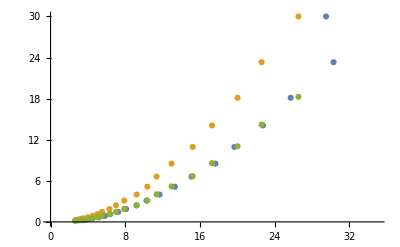

Using a single E-vs-r curve with scaling by the inner dome potential difference (vInner - vFaceplate) captures the energy dependence well up to about 15 eV. Will use the 99 V curve.

Uncertainties associated with approximating the TII MCS curves are likely not as significant as other sources of error.

What is the dependence of r vs VMcp at each energy?

```mathematica
moments99[[1,2]]
```

{781254.,2.56286,2.37032,-0.0174081,2.73326,3.12664,1.89629,0.681378,1512.14,23894.7,58934.1}

```mathematica
mcpVoltages99[[All,All]]
```

```mathematica
terms=Flatten[Outer[Times,{1,y},{1,x,x^2,x^3}]]
```

{1,x,x^2,x^3,y,x y,x^2 y,x^3 y}

```mathematica
model99=LinearModelFit[Transpose[{Flatten[moments99[[All,All,2]]],Flatten[mcpVoltages99]/(-2400.),Flatten[energies99]/99.}],terms,{x,y}]
```

FittedModel[0.00872754-0.00445482 x+«8»+8.6807×10^-6 x^3 y]

```mathematica
Normal[model99]/.x->r/.y->(vmcpN)
```

```mathematica
0.008727536876620966-0.004454815158800095 r+0.0009085603706168588 r^2-0.000014365393160422022 r^3-0.010918278041742287 vmcpN+0.004981990763549952 r vmcpN-0.00029784411180069903 r^2 vmcpN+8.680704266427428*^-6 r^3 vmcpN
```

```mathematica
energies99[[1]]
```

{0.25,0.32164,0.41381,0.532392,0.684956,0.881237,1.13377,1.45866,1.87666,2.41443,3.10632,3.99647,5.1417,6.61512,8.51076,10.9496,14.0874,18.1243,23.318,30.}

```mathematica
energies60[[1]]
```

{0.25,0.32164,0.41381,0.532392,0.684956,0.881237,1.13377,1.45866,1.87666,2.41443,3.10632,3.99647,5.1417,6.61512,8.51076,10.9496,14.0874,18.1243,23.318,30.}

```mathematica
Manipulate[Show[ListPlot[{Transpose[{moments60[[m,All,2]],energies60[[m]]}],Transpose[{moments99[[m,All,2]],energies99[[m]]}],Transpose[{moments99[[m,All,2]],energies99[[m]]/99.*60.3}]},PlotRange->{{0,35},{0,eMax}}],Plot[model99[x,mcpVoltages99[[m,1]]/(-2400)]*60.3,{x,0,35},PlotStyle->Directive[Dashed,Purple]],Plot[model99[x,vmcp/(-2400)]*99,{x,0,35},PlotStyle->Directive[Gray,Dashed]]],{m,1,Length@moments60,1},{vmcp,-2400,-1000}]
```

```mathematica
MinMax[moments60[[All,All,2]]]
```

{0.,31.5}

```mathematica
MinMax[moments99[[All,All,2]]]
```

{2.28033,27.5455}